# delta smearing

## g switch, δ smear, go futher with the transition probability

## the smearing function

```mathematica
f[x_]:=DiracDelta[x]
ftil[k_]:=FourierTransform[f[x],x,k,FourierParameters->{1,-1}]
```

#### simplify the fourier transform

```mathematica
ftil[k]
```

1

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0]
```

## the transition probability

```mathematica
ggintegrandd[k_]:=-1/(2π)ⅇ^(-ε*k-1/2*η^2*(Ω+k)^2)*(-1+α*(2+ⅇ^(2*η^2*Ω*k)))*k*ftil[k]^2
```

#### with an ε regularized cutoff (exp)

```mathematica
Integrate[ggintegrandd[k],{k,0,∞}]
```

ConditionalExpression[-(ⅇ^(-1/2 η^2 Ω^2) (ⅇ^(((ε+η^2 Ω)^2)/(2 η^2)) √(2 π) (-1+2 α) √(η^2) √(((ε-η^2 Ω)^2)/η^2) (ε+η^2 Ω)^2 Erf[(√(η^2 (ε+η^2 Ω)^2))/(√2 η^2)]+√(((ε+η^2 Ω)^2)/η^2) (-η^2 √(((ε-η^2 Ω)^2)/η^2) (2 (1-3 α) √(η^2)+ⅇ^(((ε-η^2 Ω)^2)/(2 η^2)) √(2 π) α (ε-η^2 Ω)+ⅇ^(((ε+η^2 Ω)^2)/(2 η^2)) √(2 π) (-1+2 α) (ε+η^2 Ω))+ⅇ^(((ε-η^2 Ω)^2)/(2 η^2)) √(2 π) α √(η^2) (ε-η^2 Ω)^2 Erf[(√((ε η-η^3 Ω)^2))/(√2 η^2)])))/(4 π η^4 √(η^2) √(((ε-η^2 Ω)^2)/η^2) √(((ε+η^2 Ω)^2)/η^2)),Re[η^2]>0]

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε∈Reals&&ε>0&&Ω∈Reals&&Ω>0]
```

-1/(4 π η^3 Abs[ε^2-η^4 Ω^2])ⅇ^(-1/2 η^2 Ω^2) (ⅇ^(((ε+η^2 Ω)^2)/(2 η^2)) √(2 π) (-1+2 α) (ε+η^2 Ω)^2 Abs[ε-η^2 Ω] Erf[(ε+η^2 Ω)/(√2 η)]+(ε/η+η Ω) (-η (2 (1-3 α) η+ⅇ^(((ε-η^2 Ω)^2)/(2 η^2)) √(2 π) α (ε-η^2 Ω)+ⅇ^(((ε+η^2 Ω)^2)/(2 η^2)) √(2 π) (-1+2 α) (ε+η^2 Ω)) Abs[ε-η^2 Ω]+ⅇ^(((ε-η^2 Ω)^2)/(2 η^2)) √(2 π) α η (ε-η^2 Ω)^2 Erf[Abs[ε-η^2 Ω]/(√2 η)]))

```mathematica
FullSimplify[Out[5],Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η≥0&&ε∈Reals&&ε>0&&Ω∈Reals&&Ω>0]
```

```mathematica
pertexp[η_]:=-1/(4 π η^3 (ε+η^2 Ω))ⅇ^(-1/2 η^2 Ω^2) (ⅇ^(((ε-η^2 Ω)^2)/(2 η^2)) √(2 π) α (ε^2-η^4 Ω^2) Erf[(ε-η^2 Ω)/(√2 η)]+(ε+η^2 Ω) (2 (-1+3 α) η+ⅇ^(((ε-η^2 Ω)^2)/(2 η^2)) √(2 π) (-α ε+α η^2 Ω-ⅇ^(2 ε Ω) (-1+2 α) (ε+η^2 Ω) Erfc[(ε+η^2 Ω)/(√2 η)])))
```

```mathematica
pexp[η_]:=α+λ^2*pertexp[η]
```

#### with no cutoff (ε:=0)

```mathematica
Simplify[pertexp[η],Assumptions->ε==0]
```

```mathematica
FullSimplify[1/(4 π η^2)ⅇ^(-1/2 η^2 Ω^2) (2-6 α-ⅇ^((η^2 Ω^2)/2) √(2 π) α η Ω (1+Erf[(η Ω)/(√2)])+ⅇ^((η^2 Ω^2)/2) √(2 π) (-1+2 α) η Ω Erfc[(η Ω)/(√2)]),Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&Ω∈Reals&&Ω>0]
```

(ⅇ^(-1/2 η^2 Ω^2) (2-6 α+ⅇ^((η^2 Ω^2)/2) √(2 π) η Ω (-2 α+(-1+3 α) Erfc[(η Ω)/(√2)])))/(4 π η^2)

```mathematica
pertnone[η_]:=(2 ⅇ^(-η^2/2)-√(2 π) η Erfc[η/(√2)])/(4 π η^2)
```

```mathematica
pnone[η_]:=α+λ^2*pertnone[η]
```

#### with a sharp cutoff (ε:=0 and integrate only up to a constant)

```mathematica
Integrate[ggintegrandd[k],{k,0,5*Ω}]
```

-1/(4 π η^3)(ⅇ^(-1/2 Ω (2 ε+η^2 Ω)) α (2 ⅇ^(ε Ω) η+ⅇ^((ε^2+η^4 Ω^2)/(2 η^2)) √(2 π) (ε-η^2 Ω) Erf[(ε-η^2 Ω)/(√2 η)])+ⅇ^(-1/2 η^2 Ω^2) (-1+2 α) (2 η+ⅇ^(((ε+η^2 Ω)^2)/(2 η^2)) √(2 π) (ε+η^2 Ω) Erf[(ε+η^2 Ω)/(√2 η)])+ⅇ^(-Ω (5 ε+18 η^2 Ω)) (ⅇ^(10 η^2 Ω^2) α (-2 η-ⅇ^(((ε+4 η^2 Ω)^2)/(2 η^2)) √(2 π) (ε-η^2 Ω) Erf[(ε+4 η^2 Ω)/(√2 η)])-(-1+2 α) (2 η+ⅇ^(((ε+6 η^2 Ω)^2)/(2 η^2)) √(2 π) (ε+η^2 Ω) Erf[(ε+6 η^2 Ω)/(√2 η)])))

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε==0&&Ω∈Reals]
```

```mathematica
pertsharp[η_]:=-1/(4 π η^2)(2 ⅇ^(-18 η^2 Ω^2)-2 ⅇ^(-1/2 η^2 Ω^2)-4 ⅇ^(-18 η^2 Ω^2) α-2 ⅇ^(-8 η^2 Ω^2) α+6 ⅇ^(-1/2 η^2 Ω^2) α+√(2 π) (-1+3 α) η Ω Erf[(η Ω)/(√2)]+√(2 π) α η Ω Erf[2 √2 η Ω]+√(2 π) η Ω Erf[3 √2 η Ω]-2 √(2 π) α η Ω Erf[3 √2 η Ω])
```

```mathematica
psharp[η_]:=α+λ^2*pertsharp[η]
```

#### with a different cutoff (later) (ε:=0 and cutoff[k_]:=something)

## plot p v η

#### assign the parameters numbers

```mathematica
Ω:=1
α:=1
λ:=.1
ε:=0.25
```

#### clear parameters of numbers when necessary

```mathematica
Clear[σ];Clear[Ω];Clear[α];Clear[λ];Clear[ε];
```

#### plot p v η

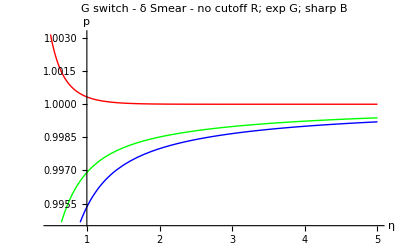

```mathematica
Plot[{pnone[η],pexp[η],psharp[η]},{η,0.5,5},
AxesLabel->{η,p},
PlotStyle->{Red,Green,Blue},
PerformanceGoal->"Quality",
PlotLabel->Style["G switch - δ Smear -\n no cutoff R; exp G; sharp B",FontSize->16]]
```

```mathematica
Limit[pnone[η],η->0]
```

∞

```mathematica
Limit[psharp[η],η->0]
```

0.0198944

```mathematica
Limit[pexp[η],η->0]
```

0.0254648

```mathematica
pexp[0]
```

Indeterminate

```mathematica
Limit[pexp[η],η->0]
```

$Aborted

```mathematica
pexp[.001]
```

1591.55

## status

sharp and no cutoff behaviour are as expected -- finite and infinite in η→0 respectively

exponential cutoff probability very ill behaved as η→0. unclear to me why. the limit as η goes to zero is finite though? but the value at zero comes out as indeterminate????

i’m not like.... super worried about this tho. but i’ll ask, it might maybe be not cool

Edu suggests that this is not too weird -- we’d explore further if we wanted to publish or something, but it’s fine for now